```mathematica
sNTM[{q_,p_}]:= {q+a(1-(p - b Sin[2 π q])^2),p-b Sin[2π q]}
```

```mathematica
stdMap[{q_,p_}]:= {q+p + b Sin[2 π q]/(2 π),p+b Sin[2π q]/(2 π)}
```

```mathematica
b=10
stdMap[{0,.5}]
stdMap[%]
stdMap[%]
stdMap[%]
stdMap[%]
stdMap[%]
stdMap[%]
stdMap[%]
stdMap[%]
stdMap[%]
```

10

{0.5,0.5}

{1.,0.5}

{1.5,0.5}

{2.,0.5}

{2.5,0.5}

{3.,0.5}

{3.5,0.5}

{4.,0.5}

{4.5,0.5}

{5.,0.5}

```mathematica
rootFunctionSNTM[{q_?NumericQ,p_?NumericQ},i_]:= Piecewise[{{Sin[2π (q-a(1-p^2)/2)],Mod[i,2]== 1},{Sin[2 π q],Mod[i,2]== 0}}]
```

Here I write code to make a contour plot of where this should be the thing I

```mathematica
SMOOTH[x_?NumericQ]:=x/(1+Abs[x])
root[{x_?NumericQ,y_?NumericQ},sln_]:= x-findX[y,sln]-Piecewise[{{(m1-1)/2,Mod[m1,2]== 1},{m1/2,Mod[m1,2]== 0}}]
findX[y_?NumericQ,sln_]:=Switch[sln,1,0,2,.5,3,a/2 * (1-y^2),4,a/2 * (1-y^2)+.5]
```

```mathematica
a = 0.6001; b=0.0336;
sNTM[{0, -0.00871008137}]
sNTM[%]
sNTM[%]
sNTM[%]
sNTM[%]
sNTM[%]
sNTM[%]
sNTM[%]
sNTM[%]
sNTM[%]
```

{0.600054,-0.00871008}

{1.20008,0.0110488}

{1.79992,-0.020912}

{2.39995,0.0110488}

{3.,-0.00871008}

{3.60005,-0.00871008}

{4.20008,0.0110488}

{4.79992,-0.020912}

{5.39995,0.0110488}

{6.,-0.00871008}

Here is a contour plot of the root function’s zeroes in (b,y) space.  The maxima is the collision point for this given a value and is how bifurcation curves are generated.

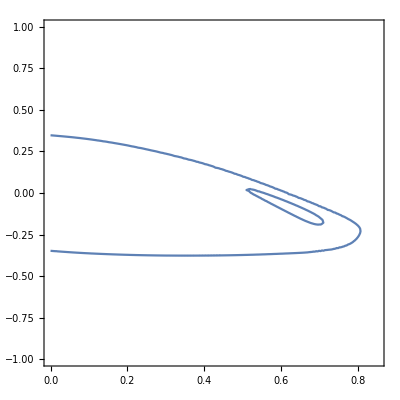

```mathematica
m2=34;m1=21;a=0.7;
ContourPlot[SMOOTH[root[Nest[sNTM,{0,p0},Piecewise[{{(m2+1)/2,Mod[m2,2]== 1},{m2/2,Mod[m2,2]== 0}}]],Switch[Mod[m1,2],1,Switch[Mod[m2,2],1,4,0,2],0,3]]]== 0,{b,0,.85},{p0,-1,1},MaxRecursion->2]
```

```mathematica
Table[{},
```

```mathematica
g[a_,b_,q0_,p0_]:=RecurrenceTable[{q[n+1]== Mod[q[n]+a(1-(p[n]-b Sin[2 π q[n]])^2),1,-1/2],p[n+1]==Mod[p[n]-b Sin[2π q[n]],1,-1/2],z[n+1]== z[n],z[0]== p0,q[0]== q0,p[0]== p0},{q,p,z},{n,500}];
```

```mathematica
Parallelize[Do[Export["pngs/standardNontwistMap/"<>"standardNontwistMap_b="<>ToString[IntegerPart[b*100]]<>".png",Graphics[{Hue[Abs[1-2#3]],PointSize[0.002],Point[{#1,#2}]}&@@@Flatten[Table[g[a,b,RandomReal[{-.5,.5}],RandomReal[{-.5,.5}]],{index,0,1000}],1],AspectRatio->1,ImageSize->1024,Prolog->{Black,Rectangle[Scaled[{0,0}],Scaled[{1,1}]]}
,PlotLabel->"a=0.615 and b="<>ToString[b],Axes->True,Frame->True]],{b,0,1,.05}]];
```

```mathematica
Graphics[{Hue[Abs[1-2#3]],PointSize[0.002],Point[{#1,#2}]}&@@@Flatten[Table[g[a,b,RandomReal[{-.5,.5}],RandomReal[{-.5,.5}]],{index,0,1000}],1],AspectRatio->1,ImageSize->1024,Prolog->{Black,Rectangle[Scaled[{0,0}],Scaled[{1,1}]]}
,PlotLabel->"a=0.s615 and b="<>ToString[b],Axes->True,Frame->True]
```